```mathematica
tv1wellen=List[367.75*10^-9,404.74*10^-9,441.47*10^-9,543.92*10^-9,581.76*10^-9]
```

{3.6775×10^-7,4.0474×10^-7,4.4147×10^-7,5.4392×10^-7,5.8176×10^-7}

```mathematica
spannungFilter1=List[0.9,0.75,0.3,0.18,0.17]
```

{0.9,0.75,0.3,0.18,0.17}

```mathematica
spannungFilter=List[0.17,0.18,0.3,0.75,0.9]
```

{0.17,0.18,0.3,0.75,0.9}

```mathematica
tv2wellen=List[940.74*10^-9,637.3*10^-9,592.16*10^-9,564.47*10^-9,403.49*10^-9]
```

{9.4074×10^-7,6.373×10^-7,5.9216×10^-7,5.6447×10^-7,4.0349×10^-7}

```mathematica
spannungDiode=List[1.05,1.62,1.75,1.83,2.82]
```

{1.05,1.62,1.75,1.83,2.82}

```mathematica
c=3*10^8
```

300000000

```mathematica
q=1.602176634*10^-19
```

1.60218×10^-19

```mathematica
tv1frequenz=(c/tv1wellen)
```

{8.15772×10^14,7.41217×10^14,6.79548×10^14,5.51552×10^14,5.15677×10^14}

```mathematica
tv2frequenz=(c/tv2wellen)
```

{3.18898×10^14,4.70736×10^14,5.0662×10^14,5.31472×10^14,7.43513×10^14}

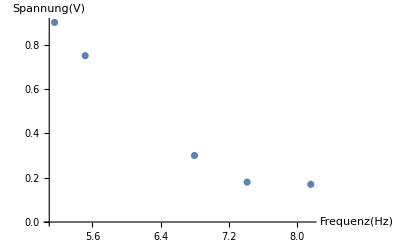

```mathematica
ListPlot[Table[{tv1frequenz[[i]],spannungFilter[[i]]},{i,1,5}],PlotRange->All,AxesLabel->{"Frequenz(Hz)","Spannung(V)"}]
```

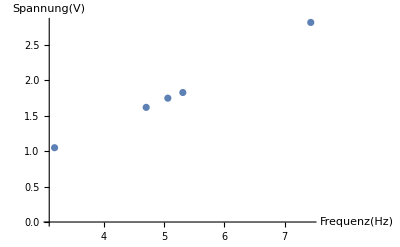

```mathematica
ListPlot[Table[{tv2frequenz[[i]],spannungDiode[[i]]},{i,1,5}],PlotRange->All,AxesLabel->{"Frequenz(Hz)","Spannung(V)"}]
```

```mathematica
tv1h=List[0,0,0,0,0]
```

{0,0,0,0,0}

```mathematica
tv2h=List[0,0,0,0,0]
```

{0,0,0,0,0}

```mathematica
For[i=1,i<5,i++,tv1h[[i]]=q*(spannungFilter[[i]]/tv1frequenz[[i]])]
```

```mathematica
tv1h
```

{3.3388×10^-35,3.89079×10^-35,7.07313×10^-35,2.17864×10^-34,2.79625×10^-34}

```mathematica
For[i=1,i<6,i++,tv2h[[i]]=q*(spannungDiode[[i]]/tv2frequenz[[i]])]
```

```mathematica
tv2h
```

{5.27531×10^-34,5.51376×10^-34,5.53435×10^-34,5.51672×10^-34,6.07675×10^-34}

```mathematica
Fit[Table[{tv2frequenz[[i]],q*spannungDiode[[i]]},{i,1,5}],{1,x},x]
```

-5.41778×10^-20+6.70519×10^-34 x

```mathematica
Fit[Table[{tv1frequenz[[i]],q*spannungFilter[[i]]},{i,1,5}],{1,x},x]
```

3.49005×10^-19-4.16654×10^-34 x

```mathematica
Fit[Table[{tv1frequenz[[i]],q*spannungFilter1[[i]]},{i,1,5}],{1,x},x]
```

-1.93627×10^-19+4.0458×10^-34 x

```mathematica
h1=LinearModelFit[Table[{tv1frequenz[[i]],q*spannungFilter1[[i]]},{i,1,5}],x,x]
```

FittedModel[-1.93627×10^-19+4.0458×10^-34 x]

```mathematica
h2=LinearModelFit[Table[{tv2frequenz[[i]],q*spannungDiode[[i]]},{i,1,5}],x,x]
```

FittedModel[-5.41778×10^-20+6.70519×10^-34 x]

```mathematica
h1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.93627×10^-19 | 5.95044×10^-20 | -3.254 | 0.047346
x | 4.0458×10^-34 | 8.8767×10^-35 | 4.55777 | 0.0197989

```mathematica
h2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.41778×10^-20 | 1.56041×10^-20 | -3.47202 | 0.0402872
x | 6.70519×10^-34 | 2.93299×10^-35 | 22.8613 | 0.00018331